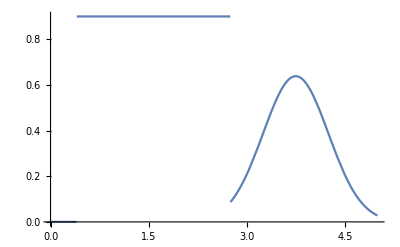

```mathematica
Clear[μ,σ]
μ:=3.750
σ:=0.5

G[x_]:=0.80Exp[-0.5(x-μ)^2/σ^2]/(σ*Sqrt[2*Pi])
f[x_]:=If[x<0.4,0,If[x<2.75,0.90,G[x]]]
Plot[f[x],{x,0,5}]
```

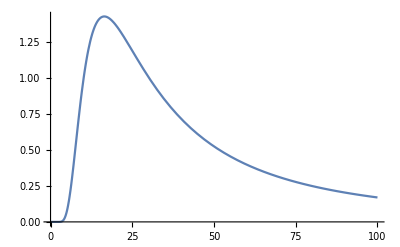

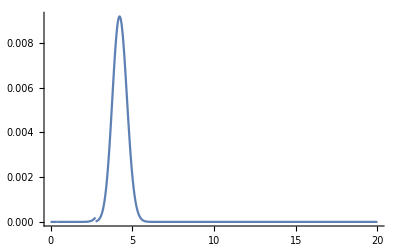

```mathematica
T:=310.15
ℏ:=6.582119624
k:=8.6173324
c:=299792458
s:=ℏ*c*2*Pi*10^{-5}/(k*T)
planck[x_]:=10^{5}/(x^3*(Exp[s/x]-1))
Plot[planck[x],{x,0,100}]
Plot[planck[x]*f[x],{x,0,20}, PlotRange->All]
```

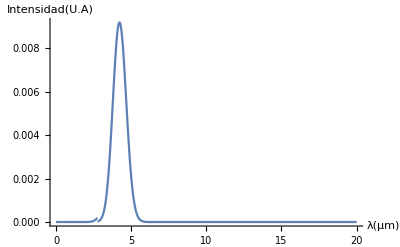

```mathematica
Show[%370,AxesLabel->{HoldForm[λ[μm]],HoldForm[Intensidad[U.A]]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```